```mathematica
A[a_]:=({{3, a, 7, 5}, {2-a, 8, 1, 6}, {2, 9, 8, a}, {a, a, a, a}});

roots=Solve[Det[A[a]]==0, a];roots = Append[roots, {a->1}];

For[i=1,i<Length[roots],i++;Print[roots⟦i⟧],Print[MatrixRank[A[a/.roots⟦i⟧]]]]

N[JordanDecomposition[A[a/.roots⟦5⟧]]⟦2⟧] //MatrixForm

Remove["Global`*"]
```

3

{a→13}

3

{a→1/2 (3-√105)}

3

{a→1/2 (3+√105)}

3

{a→1}

(-1.17681 | 0. | 0. | 0.
0. | 13.9374 | 0. | 0.
0. | 0. | 3.61971-2.43315 ⅈ | 0.
0. | 0. | 0. | 3.61971+2.43315 ⅈ)

```mathematica
Integrate[Sin[x^2+y^2]/(ⅇ^(x^2+y^2)),{y, -∞, ∞},{x, -∞, ∞}]
```

π/2

{{y[x]→ⅇ^-x C[1]+ⅇ^-x x C[2]+1/4 ⅇ^-x (-ⅇ^(2 x)-4 x+ⅇ^(2 x) x+4 x Log[x])}}

1/4 ⅇ^-x (-ⅇ^(2 x)-4 x+ⅇ^(2 x) x+4 x Log[x])

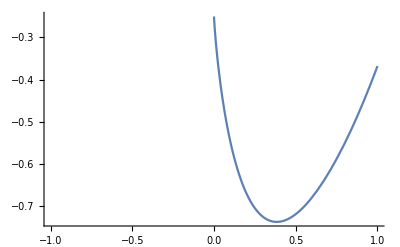

```mathematica
C1 = 0;
C2 = 0;
res=DSolve[y''[x]+2y'[x]+y[x]==x ⅇ^x+1/(x ⅇ^x),y[x],x]
defres[x_] = y[x]/.res[[1]]/.{C[1]->C1, C[2]->C2}
Plot[defres[x], {x, -1, 1}]

Clear[res,defres]
```

```mathematica
n = 10;
f[x_,y_]:=5 Sin[x*y] Cos[x+y]^3 ⅇ^(10 (x-y));
fx[n_,x_,y_] := D[f[t1,t2],{t1,n}]/.{t1->x,t2->y} //Simplify
fy[n_,x_,y_] := D[f[t1,t2],{t2,n}]/.{t1->x,t2->y} //Simplify
fx[n,π/6,π/3]

Clear[f, der1, der2]
n=.
```

400/243 ⅇ^(-5 π/3) (-4357401885 π Cos[π^2/18]+26656371 π^3 Cos[π^2/18]-18711 π^5 Cos[π^2/18]+π^7 Cos[π^2/18]-17474822550 Sin[π^2/18]+459933390 π^2 Sin[π^2/18]-916650 π^4 Sin[π^2/18]+210 π^6 Sin[π^2/18])

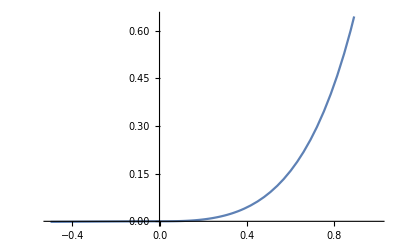

```mathematica
res =NDSolve[{x^2 y''[x]-3 x y'[x]==(6 y[x]^2)/x^2-4 y[x], y[1]==1, y'[1]==4}, y,{x, -0.5, 2}];
f=y/.res⟦1⟧;
Plot[f[s], {s, -0.5, 1}]

Clear[res, f]
```